# Homework 2

## Derek Prince APPM 2450 - 002, Fall 2015 Due 4 September, 2015

```mathematica
Clear["Global`*"];
```

## Problem 1

A.

Particle 1: x_1= 2cos(t)  y_1= 2sin(t) 0 ≤ t ≤ 2π
Particle 2: x_2 = 3cost(t)  y_2 = -1 + sin(t) 0 ≤ t ≤ 2π

```mathematica
r1[t_]={2Cos[t],2Sin[t]}; (* particle 1 *)
r2[t_]={3Cos[t],-1+Sin[t]}; (* particle 2 *)
```

```mathematica
partplot = ParametricPlot[{r1[t], r2[t]}, {t, 0, 2π}, AxesLabel->{Style["x", Bold,Medium], Style["y", Bold, Medium]}, PlotStyle-> {Red, Blue}];
```

#### B.

this

```mathematica
intersect1 = FindRoot[r1[t]==r2[s],{{t,1},{s,1}}];
intersect2=FindRoot[r1[t]==r2[s],{{t,3},{s,3}}];
col = FindRoot[r1[t]==r2[s], {{t,6}, {s, 6}}];
```

Now for the graphics...

```mathematica
circIntersect1 = Graphics[{Green, Disk[r1[t]/.intersect1, 0.20]}];
circIntersect2 = Graphics[{Green, Disk[r1[t]/.intersect2, 0.20]}];
circCol = Graphics[{Purple, Disk[r1[t]/.col, 0.25]}];
label = Graphics[{Red, Text[Style["Collision!", Large, Bold], {0,-1.4}]}];
```

#### C.

A vector velocity is a line tangent to the intersection, so I have to make an arrow graphic alligned with the derivative at the place I place it.

```mathematica
velar = Graphics[Arrow[]];
```

```mathematica
The Graph
```

Graph The

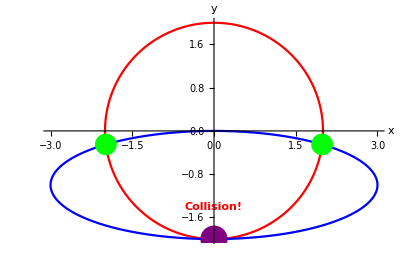

```mathematica
Show[partplot, circIntersect1, circIntersect2, circCol, label]
```